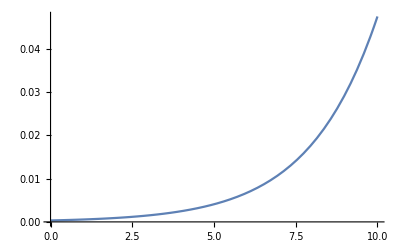

```mathematica
avgk = 8;
trophicload=2;
probext = 1/(1 + Exp[-0.5*(Np-(trophicload*avgk))]);
Plot[probext,{Np,0,10}]
```

10

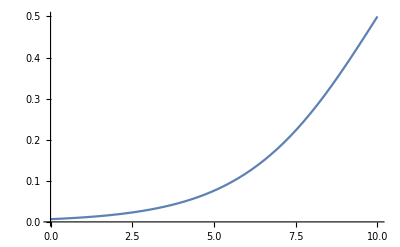

```mathematica
tl=10
probext2 = 1/(1 + Exp[-0.5*(Np-tl)]);
Plot[probext2,{Np,0,10}]
```

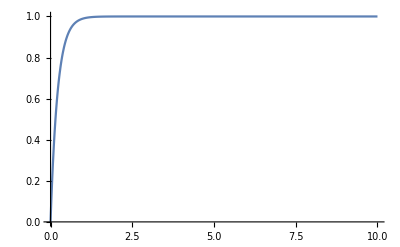

```mathematica
Plot[1-0.01^n-(1-0.01)^1000,{n,0,10},PlotRange->{0,1}]
```

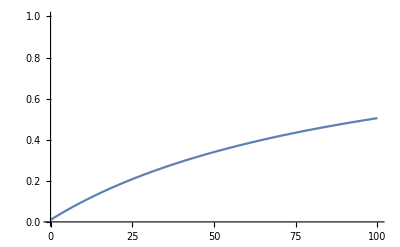

```mathematica
baseline=0.01;
Plot[baseline+ (1-baseline)*(1 - 1/(1+0.01n)),{n,0,100},PlotRange->{0,1}]
```

```mathematica
Solve[{
0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,P1,P2,R1,R2}]
```

{{R→0,P1→0,P2→0,R1→1,R2→1},{R→1,P1→0,P2→0,R1→0,R2→0},{R→1,P1→0,P2→0,R1→1,R2→0},{R→1,P1→0,P2→0,R1→1,R2→1},{R→0,P1→0,P2→0,R1→1,R2→0},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2)),R1→0,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2))},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2)),R1→1,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2))},{R→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r)/(a2^2 e2),R1→0,R2→0},{R→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r)/(a2^2 e2),R1→1,R2→0},{R→1,P1→0,P2→0,R1→0,R2→1},{R→0,P1→0,P2→0,R1→0,R2→1},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0,R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→0},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0,R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→1},{R→m1/(a1 e1),P1→((a1 e1-m1) r)/(a1^2 e1),P2→0,R1→0,R2→0},{R→m1/(a1 e1),P1→((a1 e1-m1) r)/(a1^2 e1),P2→0,R1→0,R2→1},{R→0,P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2),R1→1,R2→m2/(a2 e2)},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0,R1→m1/(a1 e1),R2→1},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0,R1→m1/(a1 e1),R2→0},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→((a2 e2-m2) r2)/(a2^2 e2),R1→m1/(a1 e1),R2→m2/(a2 e2)},{R→0,P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2),R1→0,R2→m2/(a2 e2)},{R→-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1→-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2→-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2))},{R→m1/(a1 e1),P1→-(-a1 a2 e1 e2 r+a2 e2 m1 r+a1 a2 e1 e2 r2+a2 e2 m1 r2-a1 e1 m2 r2)/(a1^2 a2 e1 e2),P2→((a1 a2 e1 e2+a2 e2 m1-a1 e1 m2) r2)/(a1 a2^2 e1 e2),R1→0,R2→-(a2 e2 m1-a1 e1 m2)/(a1 a2 e1 e2)},{R→m2/(a2 e2),P1→((a1 a2 e1 e2-a2 e2 m1+a1 e1 m2) r1)/(a1^2 a2 e1 e2),P2→-(-a1 a2 e1 e2 r+a1 e1 m2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 e1 m2 r1)/(a1 a2^2 e1 e2),R1→-(-a2 e2 m1+a1 e1 m2)/(a1 a2 e1 e2),R2→0},{R→0,P1→0,P2→0,R1→0,R2→0}}

```mathematica
FullSimplify[{R->-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1->(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2->((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1->-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2->-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2))}]
```

{R→(a2 e2 m1 r1+a1 e1 (a2 e2 (r-r1-r2)+m2 r2))/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (-a2 e2 m1 (r+r2)+a1 e1 (2 a2 e2 r+m2 r2)))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((a2 e2 m1 r1+a1 e1 (2 a2 e2 r-m2 (r+r1))) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1→(a2 e2 m1 (r+r2)+a1 e1 (-m2 r2+a2 e2 (-r+r1+r2)))/(a1 a2 e1 e2 (r+r1+r2)),R2→(-a2 e2 m1 r1+a1 e1 (m2 (r+r1)+a2 e2 (-r+r1+r2)))/(a1 a2 e1 e2 (r+r1+r2))}

```mathematica
SolP = Solve[{
(*0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,*)
0 == r*R*(1-R/k)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1/k1)-a1*R1*P1,
0 == r2*R2*(1-R2/k2)-a2*R2*P2
},{R,R1,R2}]
```

{{R→0,R1→0,R2→0},{R→(-a1 k P1-a2 k P2+k r)/r,R1→0,R2→0},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→0},{R→(-a1 k P1-a2 k P2+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→0},{R→0,R1→0,R2→(-a2 k2 P2+k2 r2)/r2},{R→(-a1 k P1-a2 k P2+k r)/r,R1→0,R2→(-a2 k2 P2+k2 r2)/r2},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2},{R→(-a1 k P1-a2 k P2+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2}}

```mathematica
SolP = Solve[{
(*0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,*)
0 == r*R*(1-R/k)-a1*R*P1-a2*R*P2 -a3*R*P3,
0 == r1*R1*(1-R1/k1)-a1*R1*P1,
0 == r2*R2*(1-R2/k2)-a2*R2*P2,
0 == r3*R3*(1-R3/k3)-a3*R3*P3
},{R,R1,R2,R3}]
```

{{R→0,R1→0,R2→0,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→0,R3→0},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→0},{R→0,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→0,R1→0,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→0,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3}}

```mathematica
Factor[(-a1 k P1-a2 k P2-a3 k P3+k r)/r]
```

(k (-a1 P1-a2 P2-a3 P3+r))/r

```mathematica
Solve[(k (-m*P+r))/r==1-m*ϵ,ϵ]
```

{{ϵ→(k m P+r-k r)/(m r)}}

```mathematica
FullSimplify[(-k m P+r-k r)/(m r)]
```

(r-k (m P+r))/(m r)

```mathematica
FullSimplify[SolP[[8]]]
```

{R→(-a1 P1-a2 P2+r)/r,R1→1-(a1 P1)/r1,R2→1-(a2 P2)/r2}

```mathematica
Sol=Solve[{
0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,R1,R2,P1,P2}]
```

{{R→0,R1→1,R2→1,P1→0,P2→0},{R→1,R1→0,R2→0,P1→0,P2→0},{R→1,R1→1,R2→0,P1→0,P2→0},{R→1,R1→1,R2→1,P1→0,P2→0},{R→0,R1→1,R2→0,P1→0,P2→0},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),R1→1,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2))},{R→m2/(a2 e2),R1→1,R2→0,P1→0,P2→((a2 e2-m2) r)/(a2^2 e2)},{R→1,R1→0,R2→1,P1→0,P2→0},{R→0,R1→0,R2→1,P1→0,P2→0},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→1,P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0},{R→m1/(a1 e1),R1→0,R2→1,P1→((a1 e1-m1) r)/(a1^2 e1),P2→0},{R→0,R1→1,R2→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2)},{R→0,R1→m1/(a1 e1),R2→1,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0},{R→0,R1→m1/(a1 e1),R2→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0},{R→0,R1→m1/(a1 e1),R2→m2/(a2 e2),P1→((a1 e1-m1) r1)/(a1^2 e1),P2→((a2 e2-m2) r2)/(a2^2 e2)},{R→0,R1→0,R2→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2)},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→0,P1→(r (2 a1 e1 r1-m1 r1))/(a1^2 e1 (r+r1)),P2→0},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),R1→0,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2))},{R→-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R1→-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2→-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2))},{R→m1/(a1 e1),R1→0,R2→0,P1→((a1 e1-m1) r)/(a1^2 e1),P2→0},{R→m1/(a1 e1),R1→0,R2→-(a2 e2 m1-a1 e1 m2)/(a1 a2 e1 e2),P1→-(-a1 a2 e1 e2 r+a2 e2 m1 r+a1 a2 e1 e2 r2+a2 e2 m1 r2-a1 e1 m2 r2)/(a1^2 a2 e1 e2),P2→((a1 a2 e1 e2+a2 e2 m1-a1 e1 m2) r2)/(a1 a2^2 e1 e2)},{R→m2/(a2 e2),R1→0,R2→0,P1→0,P2→((a2 e2-m2) r)/(a2^2 e2)},{R→m2/(a2 e2),R1→-(-a2 e2 m1+a1 e1 m2)/(a1 a2 e1 e2),R2→0,P1→((a1 a2 e1 e2-a2 e2 m1+a1 e1 m2) r1)/(a1^2 a2 e1 e2),P2→-(-a1 a2 e1 e2 r+a1 e1 m2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 e1 m2 r1)/(a1 a2^2 e1 e2)},{R→0,R1→0,R2→0,P1→0,P2→0}}

```mathematica
internalsolution = Sol[[19]]
```

{R→-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R1→-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2→-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2))}

```mathematica
FullSimplify[-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2))]
```

```mathematica
(a2 e2 m1 r1+a1 e1 (a2 e2 (r-r1-r2)+m2 r2))/(a1 a2 e1 e2 (r+r1+r2))/.{a2->a1,e2->e1,r2->r,r1->r,m2->m1}
```

(a1 e1 m1 r+a1 e1 (-a1 e1 r+m1 r))/(3 a1^2 e1^2 r)

```mathematica
FullSimplify[%]
```

-1/3+(2 m1)/(3 a1 e1)

Is the internal equilibrium stable?
Answer: given particular parameter values, it can be :) (at higher conversion efficiencies and high resource growth rates)

```mathematica
f = { e1*a1*(R+R1)*P1-m1*P1,
e2*a2*(R+R2)*P2-m2*P2,
 r*R*(1-R)-a1*R*P1-a2*R*P2,
 r1*R1*(1-R1)-a1*R1*P1,
 r2*R2*(1-R2)-a2*R2*P2};
x = {P1,P2,R,R1,R2};
```

```mathematica
Jac = D[f,{x}]/.internalsolution;
```

```mathematica
Manipulate[
Eig = N[Eigenvalues[Jac]/.{e1->E1,e2->E2,m1->M1,m2->M2,a1->A1,a2->A2,r->R,r1->R1,r2->R2}];
REig= Re[Eig];
ImEig = Im[Eig];
(*ListPlot[Transpose[{REig,ImEig}]],*)
Max[REig],
{E1,0.1,1},{E2,0.1,1},{M1,0.1,1},{M2,0.1,1},{A1,0.1,1},{A2,0.1,1},{R,0.1,3},{R1,0.1,3},{R2,0.1,3}
]
```

```mathematica
|
```

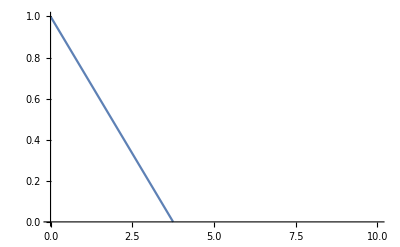

```mathematica
Nstar =1 - (numpred*a*P)/r;
Plot[Nstar/.{P->0.1,r->0.3,a->0.8},{numpred,0,10},PlotRange->{0,1}]
```

```mathematica
PrExt= Probability[-Infinity<x<0,x\[Distributed] NormalDistribution[μ,σ]]
PrExtspecific = PrExt/.μ->(1-n*ϵ)
```

1/2 Erfc[μ/(√2 σ)]

1/2 Erfc[(1-n ϵ)/(√2 σ)]

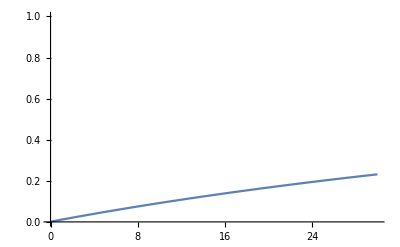

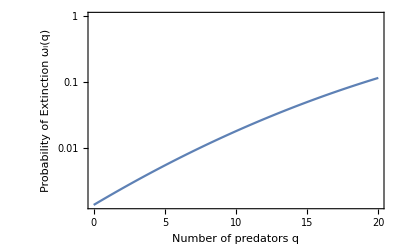

```mathematica
Plot[(ϵ*n+pb)/(1+ϵ*n)/.{pb->0.001,ϵ->0.01},{n,0,30},PlotRange->{0,1}]
PrExtPlot = LogPlot[PrExt/.{μ->1-n*ϵ/.{ϵ->0.03},σ->1/3},{n,0,20},PlotRange->{PrExtspecific/.{σ->1/3,ϵ->0.03,n->0},1},Frame->True,FrameLabel->{"Number of predators q","Probability of Extinction ω_i(q)"}]
```

```mathematica
Export["~/Dropbox/Postdoc/2014_Lego/Anime/figures/extinction.pdf",PrExtPlot]
```

~/Dropbox/Postdoc/2014_Lego/Anime/figures/extinction.pdf

1/2 Erfc[(1-n ϵ)/(√2 σ)]

```mathematica
PrExtspecific/.{σ->1/3,ϵ->0.03,n->0}
```

0.0013499

```mathematica
PrExt/.{μ->1-0*ϵ/.{ϵ->0.05},σ->0.33}
```

0.00122154

```mathematica
Solve[{
(*0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,*)
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,R1,R2}]
```

```mathematica
Conn =FullSimplify[(pi(pa/(pa+pn+pi))+pa(pi/(pa+pi+pn))) + (pn(pa/(pa+pn+pi+pm))+pa(pn/(pa+pi+pn))) + (pa(pa/(pi+pn+pa)))/.{pi->1-pa+pn+pm}]
```

1/2 (4 pa+(pa (1-2 pa+pm))/(1+pm+2 pn)-(pa+2 pa pm)/(1+2 pm+2 pn))

```mathematica
Plot3D[Conn/.{pm->0.01},{pa,0,1},{pn,0,1},AxesLabel->{"pa","pn"}]
```

-Graphics3D-